## Section | Field Quantization

We will discuss the idea of the quantization of the electromagnetic field (using the  second quantization formalism) and its application for representing quantum states of light. Then we will explore how it is implemented in Wolfram Mathematica, using the idea of a truncated Hilbert space. We will manipulate common operators and states of light, and perform calculations with them.

### Key Concepts

Quantization of electromagnetic field

Qudit representation of a field mode

Ladder operators

Vacuum fluctuations

## Quantization of a single mode field

Let’s start with the simple case of a 1D cavity  along the z axis with perfectly conducting walls at z=0 and z=L. Assuming the electric field is polarized in the x direction E(r,t) =  e_x E_x (z,t) where e_x is a unit vector along x, we also assume there are no sources of radiation (charges, currents, etc).

Maxwell equations without sources in SI units:

A single mode field  that satisfy the equations with the boundary conditions:

Where ω is the mode frequency , k is the wave number and V is the effective cavity volume . The boundary conditions allows ω_m = c (m π / L), m = 1,2,...

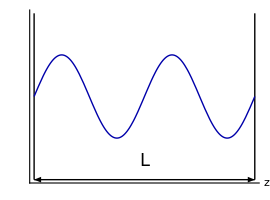

```mathematica
Show[{Graphics[{Line[{{0,-2},{0,2}}],Line[{{4Pi,-2},{4Pi,2}}],Arrowheads[{-.05,.05}],Arrow[{{0,-2},{4Pi,-2}}],Text[Style["L",18],{2Pi,-1.55}]}],Plot[Sin[x],{x,0,4Pi},PlotStyle->Directive[Darker[Blue],Thick]]},Axes->True,Ticks->None, AxesLabel->{"z",""}]
```

In a similar way the magnetic field in the cavity is B(r , t) = e_y B_y(z, t) where:

q(t)  is a time dependent function that represents canonical position and  q̇(t) = p(t) represents canonical momentum with unit mass.
The energy of the field that coincides with  Hamiltonian H is:

It can be shown  that is equivalent to an harmonic oscillator of unit mass, where p and q  are canonical momentum and position up to scaling factors

Quantizing the harmonic oscillator of unit mass promotes the canonical variables p and q to operators p̂ and q̂ that satisfy the commutation relation:

So the Hamiltonian becomes:

It is standard to introduce  non Hermitian(non observable) operators â and (â)^† which have more significance than just for sake of algebraic manipulation

Electric and magnetic field become

Where  ℰ_0 = (ℏ ω / ϵ_0 V)^(1/2) and ℬ_0 = (μ_0/k)(ϵ_0 ℏ ω^3/V)^(1/2) can be interpreted as electric and magnetic fields per photon. However, this is not really correct , because we will show a quantum state with a definite number of photons has expectation value of zero of these operators.

The â and (â)^† operators follow the commutation relation  and as a result ,   is called the number operator . Considering  |n⟩  an energy eigenstate then the eigenvalue equation  is

With energy eigenvalues:

-Graphics-

The creation and annihilation operator raises (or lower) a state to another state with an energy increase (or decrease) of  ℏω , that is why they are said to be bosonic operators that create or annihilate a photon

## Basic properties of creation and annihilation operators

In our implementation of second quantization, we approximate the infinite-dimensional Fock space by imposing a photon-number cutoff, thereby working within a finite-dimensional subspace. The cutoff, defined as the maximum occupation per mode, or globally across modes as appropriate, is user-selectable and should be chosen to balance accuracy and computational cost. This amounts to generating basis states up to the specified cutoff for each mode and constructing operators as finite matrices on the resulting tensor-product space.

Set the cut-off at 12:

```mathematica
SetFockSpaceSize[12];
```

This truncation step is, in fact, the primary approximation used to make our states and operators computationally representable. Since the Fock space is an infinite-dimensional Hilbert space, we restrict it to a finite-dimensional subspace by imposing an upper limit on the allowed excitation number.

You can call $FockSize to see the cut-off:

```mathematica
$FockSize
```

12

Show the truncated Fock-space basis.

```mathematica
QuantumBasis[$FockSize]//TraditionalForm
```

<|0→{1,0,0,0,0,0,0,0,0,0,0,0},1→{0,1,0,0,0,0,0,0,0,0,0,0},2→{0,0,1,0,0,0,0,0,0,0,0,0},3→{0,0,0,1,0,0,0,0,0,0,0,0},4→{0,0,0,0,1,0,0,0,0,0,0,0},5→{0,0,0,0,0,1,0,0,0,0,0,0},6→{0,0,0,0,0,0,1,0,0,0,0,0},7→{0,0,0,0,0,0,0,1,0,0,0,0},8→{0,0,0,0,0,0,0,0,1,0,0,0},9→{0,0,0,0,0,0,0,0,0,1,0,0},10→{0,0,0,0,0,0,0,0,0,0,1,0},11→{0,0,0,0,0,0,0,0,0,0,0,1}|>

The indexing of the basis follows the standard numbering scheme, from 0 to 1-$FockSize.

Set a as the annihilation operator:

```mathematica
a := AnnihilationOperator[];
```

The bosonic annihilation operator defined above can accept additional arguments, which will be discussed later.

Execute a:

```mathematica
a
```

QuantumOperator[…]

The above summary box represents a quantum object, here a QuantumOperator, in the Wolfram quantum framework. One can use Command+Shift+T, or Control+Shift+T, or wrapping that by TraditionalForm to see the traditional form of quantum objects.

Show the Dirac notation of a:

```mathematica
a//TraditionalForm
```

01+√2 12+√3 23+234+√5 45+√6 56+√7 67+2 √278+389+√10 910+√11 1011

Creation  and  annihilation are  non-Hermitian operators with the commutator . As one can see below, due to the truncation process, there is an edge effect (look at the last diagonal element), which is part of the error we have with the truncation:

Calculate the commutator of the annihilation and creation operators and display its matrix form.

```mathematica
Commutator[a,SuperDagger[a]]["Matrix"]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -11)

Pick an arbitrary n (within the truncation size) to verify the algebraic relations for how the annihilation and creation operators act on Fock states:

```mathematica
n = RandomInteger[{1,$FockSize -2}];
```

Verify

```mathematica
a @ FockState[n] == √n FockState[n-1]
```

True

Verify

```mathematica
SuperDagger[a] @ FockState[n] == √(n+1)FockState[n+1]
```

True

Repeated application of the annihilation operator eventually reduces any Fock state to the vacuum state, and one further application yields the scalar zero:

```mathematica
NestList[a,FockState[$FockSize -1],$FockSize]//TraditionalForm
```

{11,√11 10,√110 9,3 √1108,12 √557,12 √3856,12 √23105,60 √4624,120 √4623,360 √1542,720 √771,720 √770,0}

It is possible to construct the nth Fock state starting from the vacuum state as follows: .

Verify above relation:

```mathematica
((SuperDagger[a])^n/(√(n!)))@FockState[0] == FockState[n]
```

True

Generate the photon number operator (observable) :

```mathematica
numberOp:=SuperDagger[a]@ a
```

Check :

```mathematica
numberOp @ FockState[n] == n FockState[n]
```

True

Create a random pure state in the truncated Fock space:

```mathematica
st=QuantumState["RandomPure",$FockSize]
```

QuantumState[…]

Obtain the mean value of number operator in different ways. We will show three methods.

Bracket notation ψ a^†aψ:

```mathematica
st["Dagger"][numberOp[st]]["Scalar"]//Chop
```

4.32053

Using “Mean” property of a QuantumMeasurement:

```mathematica
(QuantumMeasurementOperator[numberOp]@st)["Mean"]
```

4.32053

Mean value by multiplying probabilities and corresponding values:

```mathematica
KeyValueMap[#1[[1]] #2 &, st["Probability"]]//Total
```

4.32053

## Quantum fluctuations for a single mode field

Electric field operator :

```mathematica
Ex := ⅈ √((h ω)/(2 Subscript[ϵ, 0] V))(a Exp[ⅈ(Dot[k,r]-ω t)]-SuperDagger[a] Exp[-ⅈ(Dot[k,r]-ω t)]);
```

The energy eigenstate |n⟩ has well defined energy but does not have a well defined value of electric field. Based on the way the ladder operators act on Fock states, is not hard to prove a state with definite number of photons has zero average field:

Verify   :

```mathematica
(SuperDagger[#]@ Ex@#)& /@ Array[FockState,$FockSize-1,0]//TraditionalForm
```

{0,0,0,0,0,0,0,0,0,0,0}

However, the mean electric field squared is not zero, hence the electric field has non zero variance for all Fock States:

```mathematica
(#["Dagger"]@(Ex@Ex) @ #)["Scalar"]& /@ Table[FockState[n],{n,0,$FockSize-2}]//FullSimplify
```

{(h ω)/(2 V ϵ_0),(3 h ω)/(2 V ϵ_0),(5 h ω)/(2 V ϵ_0),(7 h ω)/(2 V ϵ_0),(9 h ω)/(2 V ϵ_0),(11 h ω)/(2 V ϵ_0),(13 h ω)/(2 V ϵ_0),(15 h ω)/(2 V ϵ_0),(17 h ω)/(2 V ϵ_0),(19 h ω)/(2 V ϵ_0),(21 h ω)/(2 V ϵ_0)}

One can also directly find the variance with OperatorVariance with respect to Fock states:

```mathematica
Table[OperatorVariance[FockState[i],Ex],{i,0,10}]
```

{(h ω)/(2 V ϵ_0),(3 h ω)/(2 V ϵ_0),(5 h ω)/(2 V ϵ_0),(7 h ω)/(2 V ϵ_0),(9 h ω)/(2 V ϵ_0),(11 h ω)/(2 V ϵ_0),(13 h ω)/(2 V ϵ_0),(15 h ω)/(2 V ϵ_0),(17 h ω)/(2 V ϵ_0),(19 h ω)/(2 V ϵ_0),(21 h ω)/(2 V ϵ_0)}

For an operator the variance is defined as and the standard deviation or uncertainty is the square root of the variance so , for a number state we have:

Even when n = 0 the mean field is zero  but has non zero uncertainty , this phenomenon is called vacuum fluctuations. This is related to uncertainty principle because n̂ and OverHat[E_x] do not commute.

## Quadrature operators of a single mode field

Quadrature operators are defined as:

They are supported calling the following function:

```mathematica
{X1,X2}=QuadratureOperators[];
```

Quadrature operators are used to describe a state in optical phase space, and their commutation relation is very similar to canonical position and momentum

Error in last term due to truncation error:

```mathematica
Commutator[X1,X2]["Matrix"]//MatrixForm
```

(ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(11 ⅈ)/2)

However, the commutator can be derived in an exact manner using Non-Commutative Algebra functionalities (starting from version 14.3)

Define the fundamental non-commuting variables and the quadratures :

```mathematica
vars = {a,SuperDagger[a]};
{X1symb, X2symb} = {1/2(a+SuperDagger[a]), 1/(2ⅈ)(a-SuperDagger[a])};
```

Define the commutation relation:

```mathematica
rel = {Commutator[a, SuperDagger[a]]-1};
```

Reduce the commutator of the quadratures:

```mathematica
NonCommutativePolynomialReduce[Commutator[X1symb,X2symb],rel,vars][[-1]]
```

ⅈ/2

For a fock state ,the ground state |0⟩attains the minimum value  1/4:

```mathematica
Table[{OperatorVariance[FockState[n],X1],OperatorVariance[ FockState[n],X2]} ,{n,0,$FockSize-2}]
```

{{1/4,1/4},{3/4,3/4},{5/4,5/4},{7/4,7/4},{9/4,9/4},{11/4,11/4},{13/4,13/4},{15/4,15/4},{17/4,17/4},{19/4,19/4},{21/4,21/4}}

## Thermal fields

Considering  a single mode field in thermal equilibrium in a cavity at temperature T. From statistical mechanics the probability distribution  P_n that the n-th level is excited is:

where k_B is the Boltzmann constant

Using  the Hamiltonian  a mixed state described by a thermal density operator is defined based on the energy probability distribution:

The denominator is the partition function:

Energy eigenvalues:

```mathematica
Clear[n]
En = h ω (n + 1/2);
```

The partition function Z is obtained:

```mathematica
Z =Sum[Exp[-En/(kb T)],{n,0,∞}]
```

ⅇ^((h ω)/(2 kb T))/(-1+ⅇ^((h ω)/(kb T)))

The probability distribution of having a state that has n photons is:

The average photon number is :

```mathematica
Sum[n Exp[-En/(kb T)],{n,0,∞}]/Z
```

1/(-1+ⅇ^((h ω)/(kb T)))

ρ_Th can be written in terms of n^— (mean number of photons)as:

Thermal state in Wolfram QuantumFramework,  n^—=0.8:

```mathematica
ρthermal = ThermalState[0.8];
```

Visualize the density matrix:

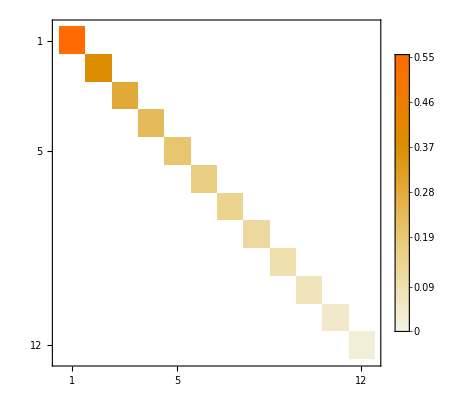

```mathematica
MatrixPlot[ρthermal["DensityMatrix"],PlotLegends->Automatic]
```

Calculate mean number of photons:

```mathematica
(QuantumMeasurementOperator[numberOp]@ρthermal)["Mean"]
```

0.799287

Use a bigger Fock space size:

```mathematica
SetFockSpaceSize[50];
```

Thermal field photon distribution varying the n^— parameter of the thermal state density matrix:

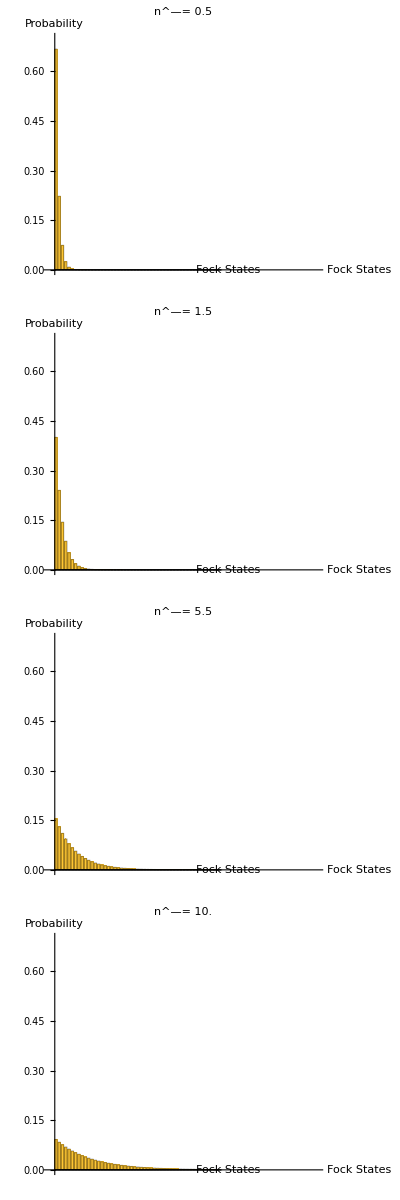

```mathematica
Table[ThermalState[x]["ProbabilitiesPlot",],{x,{0.5,1.5,5.5,10.}}]//Column
```

## The quantum phase

There have been many attempts to provide an accurate quantum description of the phase, Dirac tried to decompose creation and annihilation operators in polar form assuming a Hermitian operator ϕ exists. However, it can be shown exp( ⅈ ϕ̂) cannot be unitary ; hence ϕ̂ cannot be Hermitian. Barnett and Pegg proposed a way to build unitary operators of the form e^(ⅈ ϕ̂) , but that approach introduced non physical negative Fock states, which do not really  add any new predictions. Other issues come from the fact ϕ̂ must be an angle operator  that can lead to problematic relations when angular momentum is considered.

We will follow a formalism introduced by Susskind and Glogover, where a kind of exponential phase operator is defined and their eigenstates “phase eigenstates” serve to build a phase distribution ; and expectation values can be calculated over the phase distribution. This approach is cleaner in the calculations and can provide insight about the phase behavior of a quantum state. 
The  Susskind-Glogower operator Ê is defined by:

Set the initial default size (which is 16 when loading the paclet):

```mathematica
SetFockSpaceSize[]
```

16

Calculate Ê from the definition:

```mathematica
((SuperDagger[a]@a+1)^(-1/2))@a
```

01+12+23+34+45+56+67+78+89+910+1011+1112+1213+1314+1415

Equivalent expression for the operators are:

and  ( in each case we get N -1 terms where N is the truncated space dimensionality)

Define the operator:

```mathematica
Ephase := QuantumOperator[DiagonalMatrix[Table[1,$FockSize-1],1],$FockSize]
```

```mathematica
Ephase//TraditionalForm
```

01+12+23+34+45+56+67+78+89+910+1011+1112+1213+1314+1415

```mathematica
Ephase@SuperDagger[Ephase]//TraditionalForm
```

00+11+22+33+44+55+66+77+88+99+1010+1111+1212+1313+1414

```mathematica
SuperDagger[Ephase]@Ephase//TraditionalForm
```

11+22+33+44+55+66+77+88+99+1010+1111+1212+1313+1414+1515

Clearly the operator is not Hermitian:

```mathematica
Ephase["HermitianQ"]
```

False

Ê and (Ê)^† themselves are not observables but the operators
    and    represent  analogs of cos(ϕ) and sin(ϕ):

```mathematica
Cphase = 1/2(Ephase+SuperDagger[Ephase]);
Sphase = 1/(2ⅈ)(Ephase -SuperDagger[Ephase]);
```

Those operators are Hermitian and have commutator  (in a truncated basis this commutator has error in the last term)

```mathematica
Commutator[Cphase,Sphase]
```

ⅈ/2 00-ⅈ/21515

The known trigonometric Pythagorean identity has a close analog with a difference in the vacuum (Ĉ)^2+(Ŝ)^2 =1-1/2|0⟩⟨0| ( there is also error in the last term due to truncation):

```mathematica
(Cphase@Cphase + Sphase@Sphase)//TraditionalForm
```

1/2 00+11+22+33+44+55+66+77+88+99+1010+1111+1212+1313+1414+1/2 1515

The following commutators can be shown, that can be used to establish uncertainty relations:

```mathematica
Commutator[Cphase,numberOp] == ⅈ Sphase
```

True

```mathematica
Commutator[Sphase,numberOp]== -ⅈ Cphase
```

True

For number states  ,   and  hence

Then for n≥ 1   ΔC = ΔS = 1/(√2) and 1/2 if n = 0:

```mathematica
Partition[√OperatorVariance[FockState[#],#2]&@@@Tuples[{Range[0,$FockSize-2],{Cphase,Sphase}}],2]
```

{{1/2,1/2},{1/(√2),1/(√2)},{1/(√2),1/(√2)},{1/(√2),1/(√2)},{1/(√2),1/(√2)},{1/(√2),1/(√2)},{1/(√2),1/(√2)},{1/(√2),1/(√2)},{1/(√2),1/(√2)},{1/(√2),1/(√2)},{1/(√2),1/(√2)},{1/(√2),1/(√2)},{1/(√2),1/(√2)},{1/(√2),1/(√2)},{1/(√2),1/(√2)}}

The eigenstates |ϕ⟩ of the exponential operator hold the eigenvalue relation:
  are defined by

```mathematica
phistate := QuantumState[Table[ⅇ^(ⅈ n ϕ),{n,0,$FockSize-1}],$FockSize,"Parameters"->ϕ]
phistate//TraditionalForm
```

0+ⅇ^(ⅈ ϕ)1+ⅇ^(2 ⅈ ϕ)2+ⅇ^(3 ⅈ ϕ)3+ⅇ^(4 ⅈ ϕ)4+ⅇ^(5 ⅈ ϕ)5+ⅇ^(6 ⅈ ϕ)6+ⅇ^(7 ⅈ ϕ)7+ⅇ^(8 ⅈ ϕ)8+ⅇ^(9 ⅈ ϕ)9+ⅇ^(10 ⅈ ϕ)10+ⅇ^(11 ⅈ ϕ)11+ⅇ^(12 ⅈ ϕ)12+ⅇ^(13 ⅈ ϕ)13+ⅇ^(14 ⅈ ϕ)14+ⅇ^(15 ⅈ ϕ)15

As expected due to how Ê acts on Fock states, the last term fails in the eigenstate relation in a truncated space:

```mathematica
( Ephase@phistate-ⅇ^(ⅈ ϕ) phistate)["AmplitudesList"]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅇ^(16 ⅈ ϕ)}

Phase eigenstates resolve to unity

```mathematica
phiProj =FullSimplify[QuantumOperator[(phistate @SuperDagger[phistate]),$FockSize],Element[ϕ,Reals]];
```

```mathematica
QuantumOperator[1/(2π)Integrate[phiProj["Matrix"],{ϕ,0,2π}],$FockSize] == QuantumOperator["I"[$FockSize]]
```

True

A phase distribution 𝒫(ϕ) can be calculated for the state |ψ⟩ with the calculation recipe:

this distribution can be used to calculate average values for functions of ϕ

For any number state |n⟩ the phase distribution is 𝒫(ϕ) = 1/2π  which is a uniform distribution which has mean π and fluctuations Δϕ = π/√3, this holds for all states including vacuum

Phase distribution for Fock States:

```mathematica
Simplify[1/(2π)Abs[(phistate["Dagger"]@#)["Scalar"]]^2& /@ Array[FockState,$FockSize-1,0],ϕ∈Reals]
```

{1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π)}

Mean and standard deviation:

```mathematica
Through[{Mean,StandardDeviation}[UniformDistribution[{0,2 π}]]]
```

{π,π/(√3)}

It is possible to establish other approaches to the quantum phase, but this approach is supported by quantum estimation theory and generates a probability operator that measures maximum likelihood phase estimation. Given that is not trivial to claim there is a single correct phase operator, SG operators offer at least qualitatively a reasonable description of a quantum phase variable

## Initialization

Install  the Quantum Framework paclet:

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
```

PacletObject[…]

Load quantum framework functions:

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

Load quantum framework functions for  second quantization:

```mathematica
Needs["Wolfram`QuantumFramework`SecondQuantization`"]
```